```mathematica
(* Gamma-Gamma to Gamma-Gamma scattering at one loop level in QED *)
(* Package-X required *)
(* *)
(* mikael.mieskolainen@cern.ch, 2017 *)
Needs["X`"]

(* Precision control *)
$MaxExtraPrecision=400;
MDot[a_List,b_List]:=a[[1]]*b[[1]]-(a[[2]]*b[[2]]+a[[3]]*b[[3]]+a[[4]]*b[[4]]); (* Minkowski dot-product *)
```

Package-X v2.0.1, by Hiren H. Patel

For more information, see the

```mathematica
(* Kinematics *)
```

```mathematica
onShell=MandelstamRelations[{p1,p2,p3,p4,0,0,0,0}->{s,t,u},Eliminate->u]
```

{p1^2→0,p2^2→0,p3^2→0,p4^2→0,p1.p2→s/2,p3.p4→s/2,p1.p3→-t/2,p2.p4→-t/2,p1.p4→(s+t)/2,p2.p3→(s+t)/2}

```mathematica
photonTransversality = {LTensor[p1, μ] -> 0, LTensor[p2, ν] -> 0, LTensor[p3, ρ] -> 0, LTensor[p4, σ] -> 0}
```

{p1^μ→0,p2^ν→0,p3^ρ→0,p4^σ→0}

```mathematica
(* Define Fermion loop integrals *)
```

```mathematica
sChannelGraph = LoopIntegrate[Spur[LTensor[γ, μ], LDot[k, γ] + m*𝟙, LTensor[γ, ν], LDot[k - p2, γ] + m*𝟙, LTensor[γ, σ], 
       LDot[k + p1 - p3, γ] + m*𝟙, LTensor[γ, ρ], LDot[k + p1, γ] + m*𝟙], k, {k, m}, {k + p1, m}, {k + p1 - p3, m}, {k - p2, m}] /. 
     onShell /. photonTransversality;
```

```mathematica
tChannelGraph = LoopIntegrate[Spur[LTensor[γ, μ], LDot[k, γ] + m*𝟙, LTensor[γ, σ], LDot[k + p1 - p3 + p2, γ] + m*𝟙, LTensor[γ, ν], 
       LDot[k + p1 - p3, γ] + m*𝟙, LTensor[γ, ρ], LDot[k + p1, γ] + m*𝟙],k,{k, m},{k + p1, m},{k + p1 - p3, m},{k + p1 + p2 - p3, m}] /. onShell /. photonTransversality;
```

```mathematica
uChannelGraph =LoopIntegrate[Spur[LTensor[γ, μ], LDot[k, γ] + m*𝟙,LTensor[γ, ν], LDot[k - p2, γ] + m*𝟙, LTensor[γ, ρ],LDot[k + p3 - p2, γ] + m*𝟙, LTensor[γ, σ],LDot[k + p1, γ] + m*𝟙], k, {k, m}, {k + p1, m},{k + p3 - p2, m},{k - p2, m}] /. 
     onShell /. photonTransversality;
```

```mathematica
(* Loop factor (check documentation of LoopIntegrate[]) *)
loopfactor = ⅈ/(16*Pi^2);

total = loopfactor*(sChannelGraph + tChannelGraph + uChannelGraph);
```

```mathematica
LoopRefine[total, Part -> UVDivergent]
```

0

```mathematica
(* Massless high energy limit *)
(* bigAmp = LoopRefine[total/.m->0,TargetScale->√-t] *)
```

```mathematica
(* Full amplitude without any limit *)
bigAmp=LoopRefine[total];
```

```mathematica
(* Total polarization vector contracted amplitude *)
totalAmp=Contract[bigAmp*LTensor[e1, μ]*LTensor[e2, ν]*LTensor[e3, ρ]*LTensor[e4, σ]] // Simplify
```

-(ⅈ (24 (s+t)^2 e1.p3 e2.p3 e3.p1 e4.p3 (2 m^2 (s-t) C_0(0,0,t;m,m,m) t^3+2 (s+t)^2 t^2+8+s (s+t) (2 s^4+5 t s^3+4 t (t-2 m^2) s^2+t^2 (t-11 m^2) s+m^2 (4 m^2-3 t) t^2) D_0(0,0,0,0;s,-s-t;m,m,m,m)) s^4+80))/(48 π^2 s^4 t^4 (s+t)^4)
 |  |  |  |

```mathematica
(* Replace LDot with MDot because LDot does not evaluate explicit 4-vectors (component representation) *)
expandedAmp =totalAmp/.LDot->MDot;
expandedAmp=expandedAmp//D0Expand //C0Expand//DiscExpand;

(* Mandelstam variables and relations *)
(* s = (p1+p2)^2, t = (p1-p3)^2, u = (p1-p4)^2 *)
(* s->4E^2, t->-s/2(1-cos(theta)), u->-s/2(1+cos(theta)) *)
(* These identifications are valid for massless particles in their centre-of-mass frame *)
treplacement=Rule[t,-(s/2)*(1-Cos[theta])];
expandedAmp=expandedAmp/.treplacement;
(* expandedAmp=expandedAmp[[1]]; (* Skip the conditional rules (NOT good idea!) *) *)
```

```mathematica
(* Write explicit 4-momenta in CM-frame
p1: θ  = 0, ϕ = 0
p2: θ  = π, ϕ = π
p3: θ , ϕ = 0
p4: θ ->π - θ, ϕ = π 
with E = √s/2 *)

(* Incoming 4-momenta, p1 ~ k, p2 ~ l *)
p1=Sqrt[s]/2*{1,0,0,1};  (* Positive z-direction *)
p2=Sqrt[s]/2*{1,0,0,-1};(* Negative z-direction *)

(* Outgoing 4-momenta, p3 ~ k', p4 ~ l' *)
phi = 0;
p3=Sqrt[s]/2*{1,Sin[theta]*Cos[phi],Sin[theta]*Sin[phi],Cos[theta]};
p4={p3[[1]],-p3[[2]],-p3[[3]],-p3[[4]]};

(* Lifshitz, Pitaevskii, Relativistic Quantum Theory Part II: "124. Photon-photon scattering" *)
(* Construct pairs of polarization vectors: *)

(* Photon 1 *)
b11=Cross[{p1[[2]],p1[[3]],p1[[4]]}, {p3[[2]],p3[[3]],p3[[4]]}];
b11 = b11/Norm[b11];
b12=Cross[{p1[[2]],p1[[3]],p1[[4]]},b11]/(Sqrt[s]/2);

(* Photon 2 *)
b21 = b11;
b22 = -b12;

(* Photon 3 *)
b31 = b11;
b32 =Cross[{p3[[2]],p3[[3]],p3[[4]]},b31]/(Sqrt[s]/2);

(* Photon 4 *)
b41 = b11;
b42 = -b32;
```

```mathematica
(* Note that it is important to expand PAVE functions because otherwise trigonometric (phase wrapping) might arise while evaluating numerical values. This can be seen by inspecting amplitudes as a function of s and theta. *)
ereplacement:={e1->h1,e2->h2,e3->h3,e4->h4}; (* Notice := *)

(* Expression such as p1^2 are already in their explicit form, i.e., p_i^2=0 for all i=1,2,3,4 *)
```

```mathematica
(* Helicity amplitude 1111 *)
(* Incoming helicity *)
h1=Join[{0},b11];
h2=Join[{0},b21];
(* Outgoing helicity *)
h3=Join[{0},b31];
h4=Join[{0},b41];

(* Construct helicity amplitude *)
M1111=expandedAmp/.ereplacement;
```

```mathematica
(* Helicity amplitude 2222 *)
(* Incoming helicity *)
h1=Join[{0},b12];
h2=Join[{0},b22];
(* Outgoing helicity *)
h3=Join[{0},b32];
h4=Join[{0},b42];

(* Construct helicity amplitude, Replace LDot[] with MDot[] because those are LDot[] when package-X is active *)
M2222=expandedAmp/.ereplacement;
```

```mathematica
(* Helicity amplitude 1212 *)
(* Incoming helicity *)
h1=Join[{0},b11];
h2=Join[{0},b22];
(* Outgoing helicity *)
h3=Join[{0},b31];
h4=Join[{0},b42];

(* Construct helicity amplitude, Replace LDot[] with MDot[] because those are LDot[] when package-X is active *)
M1212=expandedAmp/.ereplacement;
```

```mathematica
(* Helicity amplitude 1221 *)
(* Incoming helicity *)
h1=Join[{0},b11];
h2=Join[{0},b22];
(* Outgoing helicity *)
h3=Join[{0},b32];
h4=Join[{0},b41];

(* Construct helicity amplitude, Replace LDot[] with MDot[] because those are LDot[] when package-X is active *)
M1221=expandedAmp/.ereplacement;
```

```mathematica
(* Helicity amplitude 1122 *)
(* Incoming helicity *)
h1=Join[{0},b11];
h2=Join[{0},b21];
(* Outgoing helicity *)
h3=Join[{0},b32];
h4=Join[{0},b42];

(* Construct helicity amplitude, Replace LDot[] with MDot[] because those are LDot[] when package-X is active *)
M1122=expandedAmp/.ereplacement;
```

```mathematica
(* Amplitude squared summed over the final polarisations and averaged over the initial polarizations *)
(* MfiAS=(1/4)*(Abs[M1111]^2+Abs[M2222]^2+2*Abs[M1212]^2+2*Abs[M1221]^2+2*Abs[M1122]^2) *)
```

```mathematica
(* Numerical substitutions *)
precision=Infinity;
```

```mathematica
mElectron=SetPrecision[0.000511,precision]; (* GeV *)
mUp =SetPrecision[0.0024,precision];
mDown =SetPrecision[0.0048,precision];

mStrange =SetPrecision[0.104,precision];
mMuon=SetPrecision[0.1057,precision];
mCharm =SetPrecision[1.27,precision];
mTau=SetPrecision[1.777,precision];

mBottom =SetPrecision[4.2,precision];
mW = SetPrecision[80.4,precision];
mTop=SetPrecision[172,precision];

massvalues={mElectron,mUp,mDown,mStrange,mMuon,mCharm,mTau,mBottom,mW,mTop};

(* QED Coupling value *)
alpha = SetPrecision[1/137.036,precision];
eQED = Sqrt[alpha*4*Pi];

(* GeV^-2 to microbarns *)
GeV2tomuBarn = SetPrecision[0.3894*10^3,precision];
```

```mathematica
(* factor 2 coming from C-symmetry (double the number of diagrams), e^4 from 4-vertices with vertex factor: i*e*gamma_mu and minus from the fermion loop *)
factor=-2eQED^4;

precision=20; (* For Mathematica arbitrary precision arithmetics *)
fM1111num=Function[{thv,sv,mv}, N[factor*M1111/.{theta->thv,s->sv,m->mv},precision]];
fM2222num=Function[{thv,sv,mv}, N[factor*M2222/.{theta->thv,s->sv,m->mv},precision]];
fM1212num=Function[{thv,sv,mv}, N[factor*M1212/.{theta->thv,s->sv,m->mv},precision]];
fM1221num=Function[{thv,sv,mv}, N[factor*M1221/.{theta->thv,s->sv,m->mv},precision]];
fM1122num=Function[{thv,sv,mv}, N[factor*M1122/.{theta->thv,s->sv,m->mv},precision]];


(* Single loop particle cross section dsigma/dOmega = 1/(64pi^2s)|M|^2 with volume element dOmega = sin(θ)*dθ*dϕ. Then we integrate over phi = [0,pi] gives us Pi and theta is left to be integrated numerically over [0,pi],only the upper hemisphere is integrated here because of two identical photons (cross section statistical factor = 0.5). *)

(* Differential cross section dσ/dcos(θ) [theta,s,m] (phi integrated over, thus multiplied with Pi at the end see above) *)
fFull=Function[{thv,sv,mv}, GeV2tomuBarn*(1/(64*Pi^2*sv))*(1/4)*(Abs[fM1111num[thv,sv,mv]]^2+Abs[fM2222num[thv,sv,mv]]^2+2*(Abs[fM1212num[thv,sv,mv]]^2+Abs[fM1221num[thv,sv,mv]]^2+Abs[fM1122num[thv,sv,mv]]^2))*Pi];

(* All fermions in the loop *)
fFullAll=Function[{thv,sv}, GeV2tomuBarn*(1/(64*Pi^2*sv))*(1/4)*(Abs[Sum[fM1111num[thv,sv,mv],{mv,massvalues}]]^2+Abs[Sum[fM2222num[thv,sv,mv],{mv,massvalues}]]^2+2*(Abs[Sum[fM1212num[thv,sv,mv],{mv,massvalues}]]^2+Abs[Sum[fM1221num[thv,sv,mv],{mv,massvalues}]]^2+Abs[Sum[fM1122num[thv,sv,mv],{mv,massvalues}]]^2))*Pi];

(* Ready to be integrated differential function with volume element derived sin(theta)*Pi *)
fFullInt=Function[{thv,sv,mv},Re[fFull[thv,sv,mv]*Sin[thv]]];

(* All loop fermions included differential cross section without interferences, i.e., we sum |M_up|^2 + |M_down|^2 + ... *)
fAll=Function[{thv,sv}, fFull[thv,sv,mUp]+fFull[thv,sv,mDown]+fFull[thv,sv,mCharm] +fFull[thv,sv,mStrange] +fFull[thv,sv,mBottom] +fFull[thv,sv,mElectron] +fFull[thv,sv,mMuon]+fFull[thv,sv,mTau]];
```

```mathematica
(* Create C-code output *)
(* CForm[Abs[Sum[fM1111num[thv,sv,mv],{mv,massvalues}]]^2] *)
```

```mathematica
(* Plot styling *)
ColorData[90,"ColorList"]
SetOptions[Plot,PlotStyle->ColorData[90,"ColorList"]];
SetOptions[Plot,PlotStyle->Thickness[0.001]];
```

{Hue[0.22, 1, 0.6],Hue[0.01, 0.8, 0.8],Hue[0.61, 0.75, 1],Hue[0.11, 1, 0.75],Hue[0.67, 0.6, 0.9],Hue[0.17, 1, 0.5],Hue[0.06, 1, 0.75],Hue[0.8, 0.5, 0.6],Hue[0.25, 1, 0.5],Hue[0.58, 0.67, 0.75]}

```mathematica
(* Lets create a list of amplitude functions to be called *)
fnames={fM1111num,fM2222num,fM1212num,fM1221num,fM1122num};
labels={"M_1111","M_2222","M_1211","M_1221","M_1122"};
```

```mathematica
Logspace[a_,b_,n_]:=10^Range[a,b,(b-a)/(n-1)];
Linspace[a_,b_,n_]:=Range[a,b,(b-a)/(n-1)];
```

```mathematica
(* Plot dsigma/dcos(theta) as a function of sqrt[s] for different fixed theta angles *)

x=Logspace[-5,3,70];
thetavalues={Pi/2,Pi/4,Pi/16};
y1=Parallelize[Table[fFull[thetavalues[[1]],sqrtsv^2,mElectron],{sqrtsv,x}]];
y2=Parallelize[Table[fFull[thetavalues[[2]],sqrtsv^2,mElectron],{sqrtsv,x}]];
y3=Parallelize[Table[fFull[thetavalues[[3]],sqrtsv^2,mElectron],{sqrtsv,x}]];
```

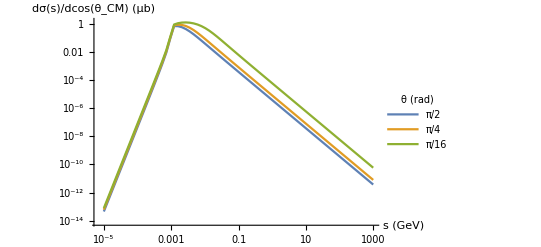

```mathematica
plot1=ListLogLogPlot[{Table[{x[[i]],y1[[i]]},{i,1,Length[x]}], Table[{x[[i]],y2[[i]]},{i,1,Length[x]}],Table[{x[[i]],y3[[i]]},{i,1,Length[x]}]},Joined->True,AxesLabel->{"s (GeV)","dσ(s)/dcos(θ_CM) (μb)"},PlotLegends->LineLegend[thetavalues,LegendLabel->"θ (rad)"]]
```

```mathematica
Export[NotebookDirectory[]<>"../figs/dsigma_s.pdf",plot1];
```

```mathematica
(* Test the all particles in the loop *)
x=Logspace[-3,3,350];
thetavalues={Pi/2, Pi/32};
y1=Parallelize[Table[fFullAll[thetavalues[[1]],sqrtsv^2],{sqrtsv,x}]];
y2=Parallelize[Table[fFullAll[thetavalues[[2]],sqrtsv^2],{sqrtsv,x}]];
```

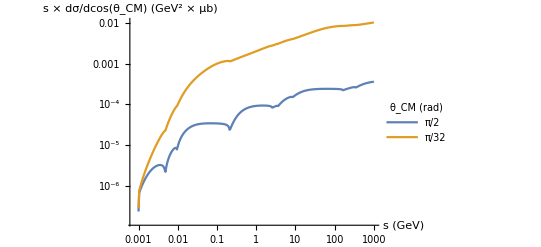

```mathematica
plot1All=ListLogLogPlot[{Table[{x[[i]],x[[i]]^2*y1[[i]]},{i,1,Length[x]}], Table[{x[[i]],x[[i]]^2*y2[[i]]},{i,1,Length[x]}]},Joined->True,AxesLabel->{"s (GeV)","s × dσ/dcos(θ_CM) (GeV^2 × μb)"},PlotLegends->LineLegend[thetavalues,LegendLabel->"θ_CM (rad)"]]
```

```mathematica
Export[NotebookDirectory[]<>"../figs/dsigma_s_All.pdf",plot1All];
```

```mathematica
(* LogLogPlot[fAll[π/2,sqrtsv^2],{sqrtsv,10^(-4),20},AxesLabel->{"s (GeV)","dσ(s)/dcos(θ_CM) |θ = π/2 (μb/1)"},PlotPoints->10] *)
```

```mathematica
(* For integration: Minimum and maximum theta angle in radians *)
costhetamin = Cos[2*Pi*150/360];
costhetamax = Cos[2*Pi*30/360];

(*plotInt=LogLogPlot[NIntegrate[fFullInt[ArcCos[costhetav],sqrtsv^2,mElectron],{costhetav,costhetamin, costhetamax}],{sqrtsv,mElectron*0.5,mElectron*100}, AxesLabel->{"s (GeV)","σ (μb) | 30 deg < θ_CM < 150 deg"},PlotPoints->10]*)
```

```mathematica
(*Export[NotebookDirectory[]<>"../figs/sigmaint.pdf",plotInt];*)
```

```mathematica
(* Sqrt[s] and theta values *)
sqrtsvalues=Logspace[-3,1,6];
thetavalues=Linspace[Pi/32,Pi-Pi/32,50];
```

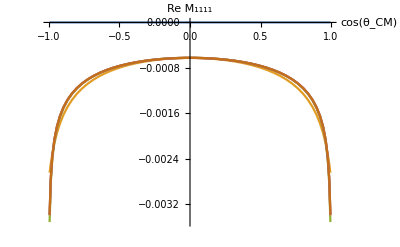
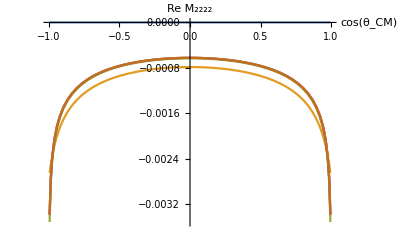
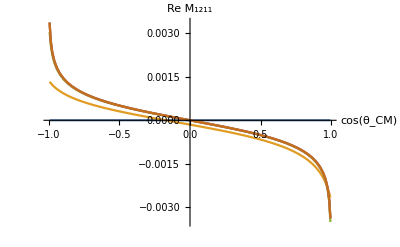
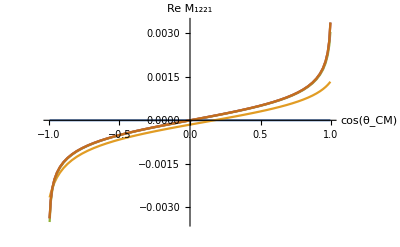
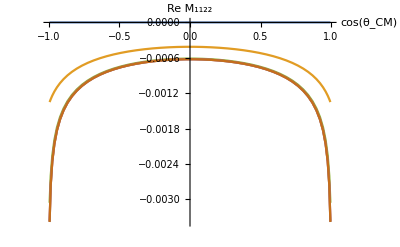

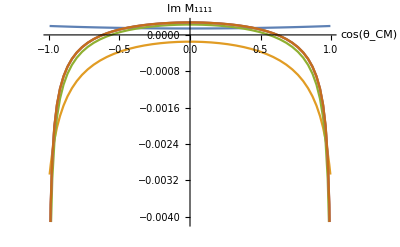
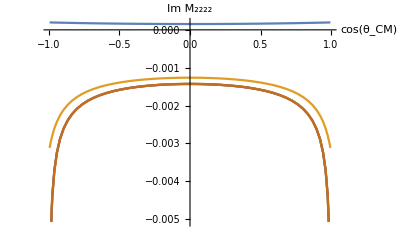
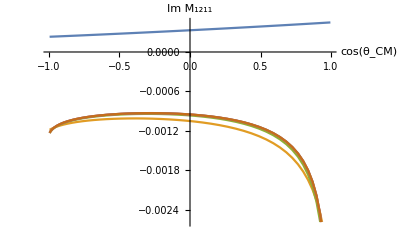

```mathematica
(* Real, Imaginary and Abs^2 for different helicity amplitudes *)
plotReal=Table[ListPlot[Table[Parallelize[Table[{Cos[thetavalues[[i]]],Re[fnames[[f]][thetavalues[[i]],sqrtsvalues[[j]]^2,mElectron]]},{i,1,Length[thetavalues]}]],{j,1,Length[sqrtsvalues]}],Joined->True,AxesLabel->{"cos(θ_CM)", "Re "<>labels[[f]]},AxesOrigin->{0,0}],{f,1,Length[fnames]}]
plotImag=Table[ListPlot[Table[Parallelize[Table[{Cos[thetavalues[[i]]],Im[fnames[[f]][thetavalues[[i]],sqrtsvalues[[j]]^2,mElectron]]},{i,1,Length[thetavalues]}]],{j,1,Length[sqrtsvalues]}],Joined->True,AxesLabel->{"cos(θ_CM)", "Im "<>labels[[f]]},AxesOrigin->{0,0}],{f,1,Length[fnames]}]
plotAbs2=Table[ListPlot[Table[Parallelize[Table[{Cos[thetavalues[[i]]],Abs[fnames[[f]][thetavalues[[i]],sqrtsvalues[[j]]^2,mElectron]]^2},{i,1,Length[thetavalues]}]],{j,1,Length[sqrtsvalues]}],Joined->True,AxesLabel->{"cos(θ_CM)", "|"<>labels[[f]]<>"|^2"},AxesOrigin->{0,0}],{f,1,Length[fnames]}]
```

```mathematica
Export[NotebookDirectory[]<>"../figs/MRe.pdf",plotReal];
Export[NotebookDirectory[]<>"../figs/MIm.pdf",plotImag];
Export[NotebookDirectory[]<>"../figs/MAbs2.pdf",plotAbs2];
```

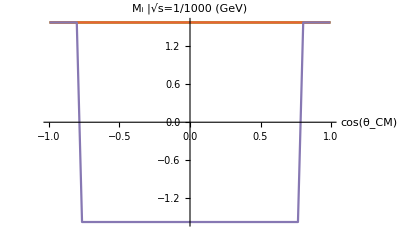
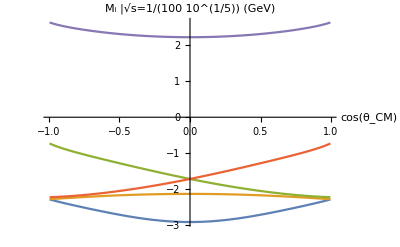
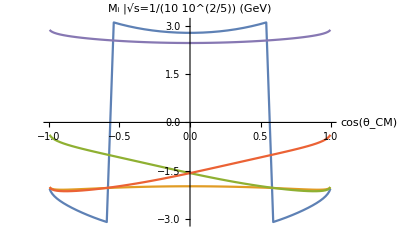
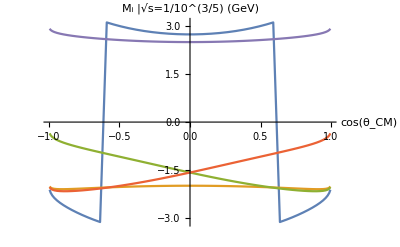
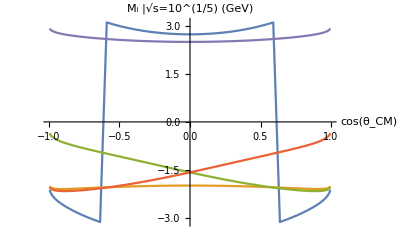
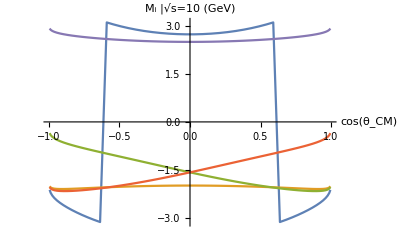

```mathematica
(* Plot Arg(M) for different helicity combinations *)
plotMArg=Table[ListPlot[Table[Parallelize[Table[{Cos[thetavalues[[i]]],Arg[fnames[[f]][thetavalues[[i]],sqrtsvalues[[j]]^2,mElectron]]},{i,1,Length[thetavalues]}]],{f,1,Length[fnames]}],Joined->True,AxesLabel->{"cos(θ_CM)", StringForm["M_i |√s=`` (GeV)",NumberForm[sqrtsvalues[[j]],2]]},AxesOrigin->{0,0}],{j,1,Length[sqrtsvalues]}]
```

```mathematica
Export[NotebookDirectory[]<>"../figs/MArg.pdf",plotMArg];
```

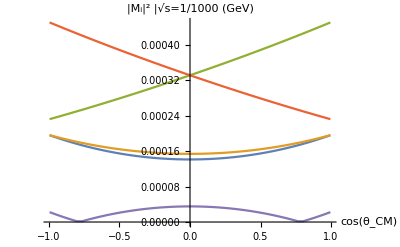
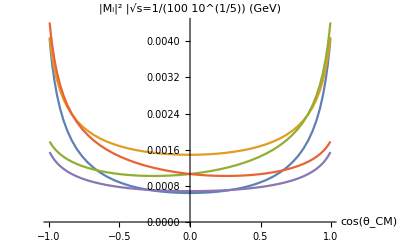
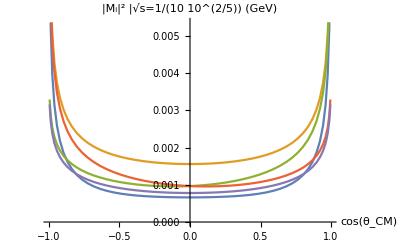
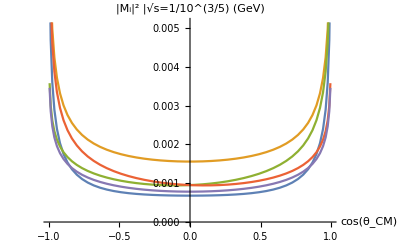
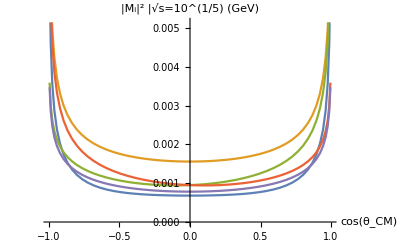
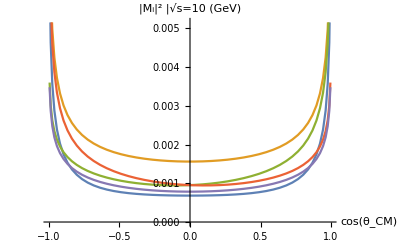

```mathematica
(* Plot |M|^2 for different helicity combinations *)
plotM2=Table[ListPlot[Table[Parallelize[Table[{Cos[thetavalues[[i]]],Abs[fnames[[f]][thetavalues[[i]],sqrtsvalues[[j]]^2,mElectron]]},{i,1,Length[thetavalues]}]],{f,1,Length[fnames]}],Joined->True,AxesLabel->{"cos(θ_CM)", StringForm["|M_i|^2 |√s=`` (GeV)",NumberForm[sqrtsvalues[[j]],2]]},AxesOrigin->{0,0}],{j,1,Length[sqrtsvalues]}]
```

```mathematica
Export[NotebookDirectory[]<>"../figs/M2.pdf",plotM2];
```

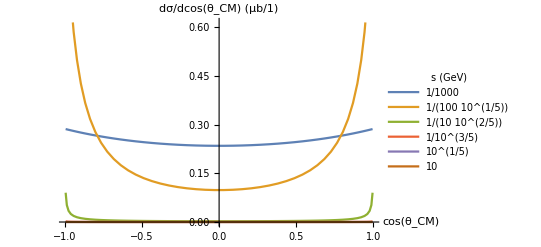

```mathematica
(* Plot dσ/dcos(θ) for different Sqrt[s] *)
plotdsigmadtheta=ListPlot[Table[Parallelize[Table[{Cos[thetavalues[[i]]],fFull[thetavalues[[i]],sqrtsvalues[[j]]^2,mElectron]},{i,1,Length[thetavalues]}]],{j,1,Length[sqrtsvalues]}],Joined->True,AxesLabel->{"cos(θ_CM)","dσ/dcos(θ_CM) (μb/1)"},PlotLegends->LineLegend[Table[sqrtsv,{sqrtsv,sqrtsvalues}],LegendLabel->"s (GeV)"]]
```

```mathematica
Export[NotebookDirectory[]<>"../figs/dsigmadcostheta.pdf",plotdsigmadtheta];
```

```mathematica
(* Plot "Transfer functions" for different theta angles *)
sqrtslist=Logspace[-4,2,250];
thetalist={Pi/2,Pi/4,Pi/16, Pi/64};

For[k=1,k<Length[thetalist]+1,k++,
plotAbsReIm=Table[
ListLogLogPlot[{
Parallelize[Table[{sqrtslist[[i]],Abs[fnames[[f]][thetalist[[k]],sqrtslist[[i]]^2,mElectron]]^2},{i,1,Length[sqrtslist]}]],Parallelize[Table[{sqrtslist[[i]],Re[fnames[[f]][thetalist[[k]],sqrtslist[[i]]^2,mElectron]]^2},{i,1,Length[sqrtslist]}]],Parallelize[Table[{sqrtslist[[i]],Im[fnames[[f]][thetalist[[k]],sqrtslist[[i]]^2,mElectron]]^2},{i,1,Length[sqrtslist]}]]},Joined->True,AxesLabel->{"s (GeV)",StringForm["``|θ =`` (rad)",labels[[f]],NumberForm[thetalist[[k]],2]]}
]
,{f,1,Length[fnames]}
];
Export[NotebookDirectory[]<>"../figs/AbsReIm"<>ToString[k]<>".pdf",plotAbsReIm];
]
```